## INTRO

💡 This is a program for χ^2 fitting, using SN1a data.
💡 SN data are taken from http://supernova.lbl.gov/Union/
💡 
💡
💡

## PRE

### Settings

Include the packages needed.

```mathematica
Needs["ErrorBarPlots`"]
<<PhysicalConstants`
```

```mathematica
Needs["PlotLegends`"]
```

Set work directory. Modify it to your own directory before runing this program. DATA folder are placed in this directory. DATA folder should contain the SN data files.

```mathematica
SetDirectory["E:\\Nutshare\\Store\\Projects\\DataFitting"];
```

### Conventions, parameters, etc

Line element: ds^2=-dt^2+a[t]^2(dr^2/(1-k r^2)+r^2(dθ^2+Sin[θ]^2 dϕ^2))

Ωm0: matter fraction
Ωd0: dark energy/cosmological constant fraction
Ωr0: radiation fraction

Ωm0w: matter fraction given by WMAP
Ωd0w: dark energy/cosmological constant fraction given by WMAP
Ωr0w: radiation fraction given WMAP

```mathematica
Ωm0w=0.27;
Ωd0w=0.73;
Ωr0w =8.09*10^-5;
```

### Basic Equations in LCDM

H0: Hubble constant in unit of km/s/Mpc
c: speed of light

```mathematica
H0w=71;
c=SpeedOfLight*Second/(1000Meter)
gra=GravitationalConstant
```

149896229/500

(6.67428×10^-11 Meter^2 Newton)/Kilogram^2

## LCDM Model

### Basic Definations

hubble[Ωm0_,Ωd0_,Ωk0_,z_]: Hubble functions in LCDM.
H[z]: an example of hubble function with given parameters.

```mathematica
hubble[Ωm0_,Ωd0_,Ωk0_,z_]:=H0w √(Ωm0(1+z)^3+Ωd0+Ωk0(1+z)^2);
H[z_]=hubble[Ωm0w,Ωd0w,0,z];
```

q[Ωm0_,Ωd0_,Ωk0_,z_]:Deceleration parameter. DEF: q[Ωm0_,Ωd0_,Ωk0_,z_]=-1/H[z]D[D[a[t],t],t]/D[a[t],t]

```mathematica
q[Ωm0_,Ωd0_,Ωk0_,z_]=-1+(1+z)/hubble[Ωm0,Ωd0,Ωk0,z] D[hubble[Ωm0,Ωd0,Ωk0,z],z];
```

```mathematica
q[Ωm0,Ωd0,Ωk0,0]
```

-1+(2 Ωk0+3 Ωm0)/(2 (Ωd0+Ωk0+Ωm0))

```mathematica
-1+(2 Ωk0+3 Ωm0)/(2 (Ωd0+Ωk0+Ωm0))
```

-1+(2 Ωk0+3 Ωm0)/(2 (Ωd0+Ωk0+Ωm0))

```mathematica
Limit[q[Ωm0,Ωd0,Ωk0,z],z->Infinity]
```

1/2

(General) Friedmann equations are

(3(a[t]'+k))/a[t]^2=8 π G ρ
2(a[t]'')/a[t]+(a[t]'+k)/a[t]^2=-8π G p

Since “zt” will be used as a parameter in most cases, we define “ztr” as a name for transition redshift, “ztrr” for transition redshift with a parameter r.
ztr[Ωm0_,Ωd0_,z_]: Transition redshift in LCDM with Ωk0 not zero with full parameters
ztrr[r_,z_]: with r=Ωm0/Ωd0

```mathematica
ztr[Ωm0_,Ωd0_]=(2 Ωd0/Ωm0)^(1/3)-1;
ztrr[r_]=(2/r)^(1/3)-1;
```

Regard “zt” as a paramter, solve out Ωd0 and Ωk0=1-Ωm0-Ωd0

Ωd0=1/2 Ωm0(1+zt)^3
Ωk0=1-Ωm0-1/2 Ωm0(1+zt)^3

### Transition redshift, deceleration parameter, theoretically.

#### Deceleration parameter

Deceleration parameter can be ploted with respect to redshift z.
Using flat FRW model. That is Ωk0=0.

```mathematica
pldec[Ωm0v_,color_]:=Plot[q[Ωm0v,1-Ωm0v,0,z],{z,-1,10},PlotRange->{{-1.05,10},{-1.05,0.55}},PlotStyle->color,AxesOrigin->{-1,0},AxesLabel->{z,q}]
```

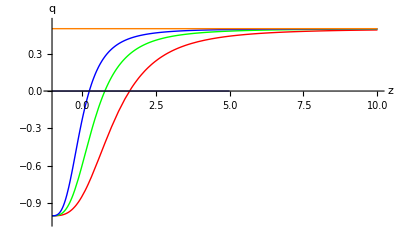

```mathematica
Show[{pldec[0.1,Red],pldec[0.26,Green],pldec[0.5,Blue],pldec[1,Orange],Plot[0,{z,-1,5},PlotStyle->Thick]}]
```

```mathematica
Manipulate[pldec[Ωm0v,{Orange,Thick}],{{Ωm0v,0.26,"Matter Fraction"},0,1,Appearance->"Open"},SaveDefinitions->True]
```

Plot deceleration parameter with respect to r. This is not related to Ωk0, i.e., the curvature of the spacetime won’t affect this result.

```mathematica
plztr[color_]:=Plot[ztr[Ωm0,1-Ωm0],{Ωm0,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->color,AxesOrigin->{0,-1}]
```

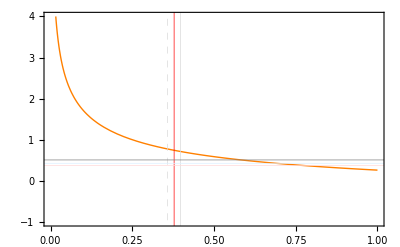

```mathematica
pldecrr=Plot[ztrr[r],{r,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}}]
```

In a flat universe, Ωk0=0. Then Ωd0=1-Ωm0.

```mathematica
pldecr=Show[Plot[ztr[Ωm0,1-Ωm0],{Ωm0,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}}],Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True]]
```

-Graphics-

## Interacting Models

### Take the form Q_c=ξ H ρ_d. I2 model

Hubble function without curvature

```mathematica
hubbleI2CC[H0_,Ωd0_,Ωm0_,w_,ξ_,z_]:=H0 √(Ωm+Ωd);
```

Conventions:
parameters : H0, Ωm0, Ωd0, w, ξ, z.

### Constant ξ + CPL w. I2CPL model.

#### Definations

CPL EoS w=w0+w1 z/(1+z)

In the following calculation, some complex numbers will occur. But

Prepare

```mathematica
hubblecmpintI2CCPL[w0_,w1_,ξI2CCPL_,z_?NumberQ]:=NIntegrate[Exp[3 w1/(1+tmp)-3w1](1+tmp)^(3(w0+w1)+ξI2CCPL-1),{tmp,0,z}]
```

```mathematica
hubblecmpintI2CCPL[-1,0.1,0.1,10]//Timing
Re[%]
```

{0.047,0.353978}

{0.047,0.353978}

Matter density

```mathematica
ΩmI2CCPL[Ωd0I2CCPL_,Ωm0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]=Ωm0I2CCPL (1+z)^3-ξI2CCPL Ωm0I2CCPL (1+z)^3 hubblecmpintI2CCPL[w0I2CCPL,w1I2CCPL,ξI2CCPL,z];
```

```mathematica
ΩdI2CCPL[Ωd0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]:=Ωd0I2CCPL Exp[-3 w1I2CCPL] Exp[3 w1I2CCPL/(1+z)](1+z)^(3(1+w0I2CCPL+w1I2CCPL)+ξI2CCPL);
```

Hubble function.

```mathematica
hubbleI2CCPL[H0I2CCPL_,Ωd0I2CCPL_,Ωm0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]=H0I2CCPL√(ΩmI2CCPL[Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]+ΩdI2CCPL[Ωd0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]);
```

```mathematica
hubbleDI2CCPL[H0I2CCPL_,Ωd0I2CCPL_,Ωm0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]=D[hubbleI2CCPL[H0I2CCPL,Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z],z];
```

```mathematica
hubbleI2CCPL[H0w,0.7,0.3,-1,0.1,0.1,10]//Timing
Re[%]
hubbleDI2CCPL[H0w,0.7,0.3,-1,0.1,0.1,10]//Timing
Re[%]
```

{0.015,1395.93}

{0.015,1395.93}

{0.5,189.745}

{0.5,189.745}

Check whether this hubble function is reasonable.

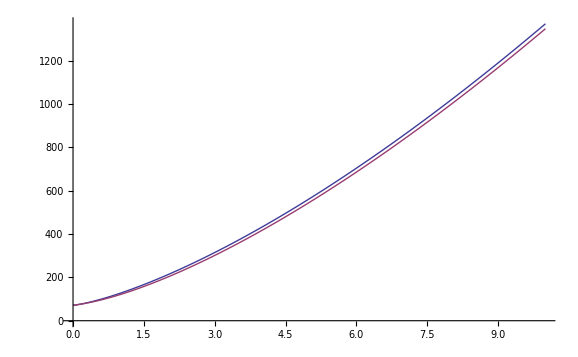
{1.7,-Graphics-}

```mathematica
Plot[{hubbleI2CCPL[H0w,0.73,0.27,-1,0.6,-0.02,z],hubble[Ωm0w,Ωd0w,0,z]},{z,0,10}]//Timing
```

Deceleration parameter

```mathematica
qI2CCPL[H0I2CCPL_,Ωd0I2CCPL_,Ωm0I2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]=-1+(1+z)/hubbleI2CCPL[H0I2CCPL,Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]hubbleDI2CCPL[H0I2CCPL,Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z];
```

```mathematica
qI2CCPL[H0w,0.7,0.3,-1,0.1,-0.1,10]//Timing
```

{0.531,0.497101}

#### Equation of State

```mathematica
plEoSI2CCPLMan=plEoSICCPLMan
```

plEoSICCPLMan

```mathematica
plEoSPhaseI2CCPL=plEoSPhaseICCPL
```

plEoSPhaseICCPL

#### Plot deceleration parameter and

```mathematica
pldecI2CCPL[Ωm0I2CCPL_,ξI2CCPL_,w0I2CCPL_,w1I2CCPL_,color_]:=Plot[Re[qI2CCPL[H0w,1-Ωm0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]],{z,-1,20},PlotRange->{{-1.05,20},{-1.05,1}},PlotStyle->color,AxesOrigin->{-1,0},AxesLabel->{z,q}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {-0.999404709003963}. NIntegrate obtained -1.04884263627452×10^17544 + 1.40986×10^-43\ ⅈ and 1.03382185950901×10^17544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {-0.99961372076828}. NIntegrate obtained -1.47122858313431×10^19005 + 3.08154×10^-22\ ⅈ and 1.48637850871999×10^19005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {-0.999542195294199}. NIntegrate obtained -1.22869741189404×10^91477 + 2.87373×10^-15\ ⅈ and 1.21110088320793×10^91477 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

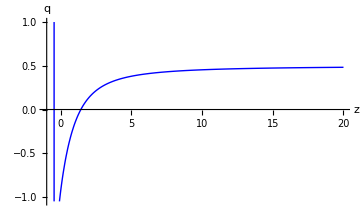
{196.311,-Graphics-}

```mathematica
pldecI2CCPL[0.1,-0.1,-1.02,0.60,Blue]//Timing
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {-0.99961372076828}. NIntegrate obtained -3.04359217687455×10^19006 + 8.05208×10^-22\ ⅈ and 3.07493346232903×10^19006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {-0.999542195294199}. NIntegrate obtained -4.07297348960766×10^91478 + 6.66305×10^-15\ ⅈ and 4.01464326594654×10^91478 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tmp near {tmp} = {-1.00154}. NIntegrate obtained -3.90883554950518×10^12675 + 1.74761×10^-11\ ⅈ and 3.85285599244719×10^12675 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

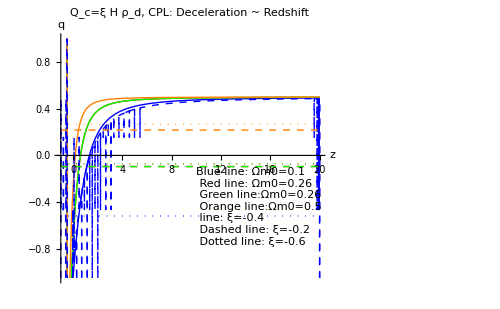

```mathematica
pldecI2CCPLShowSum=Show[{pldecI2CCPL[0.1,-0.4,-1.02,0.60,Blue],pldecI2CCPL[0.26,-0.4,-1.02,0.60,Red],pldecI2CCPL[0.26,-0.4,-1.02,0.60,Green],pldecI2CCPL[0.5,-0.4,-1.02,0.60,Orange],pldecI2CCPL[0.1,-0.2,-1.02,0.60,Directive[Blue,Dashed]],pldecI2CCPL[0.26,-0.2,-1.02,0.60,Directive[Red,Dashed]],pldecI2CCPL[0.26,-0.2,-1.02,0.60,Directive[Green,Dashed]],pldecI2CCPL[0.5,-0.2,-1.02,0.60,Directive[Orange,Dashed]],pldecI2CCPL[0.1,-0.6,-1.02,0.60,Directive[Blue,Dotted]],pldecI2CCPL[0.26,-0.6,-1.02,0.60,Directive[Red,Dotted]],pldecI2CCPL[0.26,-0.6,-1.02,0.60,Directive[Green,Dotted]],pldecI2CCPL[0.5,-0.6,-1.02,0.60,Directive[Orange,Dotted]]},Epilog->Inset[Framed[Style["Blue line: Ωm0=0.1\n Red line: Ωm0=0.26\n Green line:Ωm0=0.26\n Orange line:Ωm0=0.5\n line: ξ=-0.4\n Dashed line: ξ=-0.2\n Dotted line: ξ=-0.6",10],Background->LightGreen,FrameStyle->None],{10,-0.1},{Left,Top}],PlotLabel->"Q_c=ξ H ρ_d, CPL: Deceleration ~ Redshift",ImageSize->500]
```

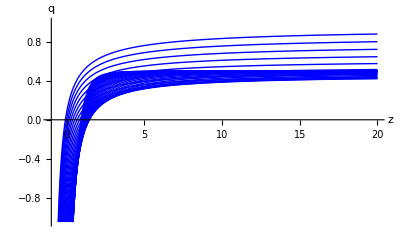
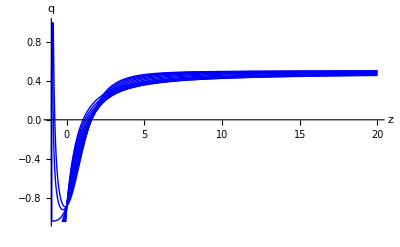
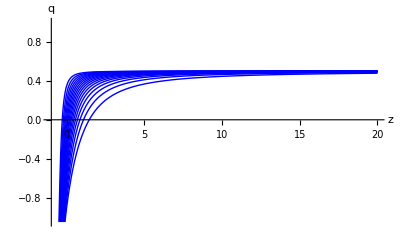
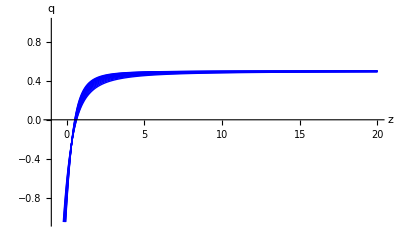
Q_c=ξ H ρ_d, CPL |  |  | 
Varying CPL w0 | Varying CPL w1 | Varying Ωm0 | Varying ξ
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
varyingI2CCPLShowSum=Grid[{{"Q_c=ξ H ρ_d, CPL",SpanFromLeft},{"Varying CPL w0","Varying CPL w1","Varying Ωm0","Varying ξ"},{Show[Table[pldecI2CCPL[0.1,-0.02,w0I2CCPL,0.6,Blue],{w0I2CCPL,-2,-0.3,0.05}]],Show[Table[pldecI2CCPL[0.1,-0.02,-1.02,w1I2CCPL,Blue],{w1I2CCPL,-0.2,1,0.1}]],Show[Table[pldecI2CCPL[Ωm0I2CCPL,-0.02,-1.02,0.6,Blue],{Ωm0I2CCPL,0.1,0.9,0.05}]],Show[Table[pldecI2CCPL[0.27,ξI2CCPL,-1.02,0.6,Blue],{ξI2CCPL,-1,0,0.1}]]}},Frame->All,Background->{{None},{LightGreen,None}}]
```

```mathematica
pldecI2CCPLManSum=Manipulate[Show[{pldecI2CCPL[Ωm0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL,Orange],pldec[Ωm0I2CCPL,{Pink,Thick}]},PlotLabel->"Q_c=ξ H ρ_d,CPL: Deceleration ~ Redshift"],{{Ωm0I2CCPL,0.26,"Matter Fraction"},0,1,Appearance->"Open"},{{ξI2CCPL,-0.4,"Interaction"},-1,0,Appearance->"Open"},{{w0I2CCPL,-1.02,"CPL EoS w0"},-2,-0.3,Appearance->"Open"},{{w1I2CCPL,0.6,"CPL EoS w1"},-0.2,1,Appearance->"Open"},Delimiter,Style["Pink is the deceleration parameter for LCDM.",Medium],Style["Orange is for interacting CPL model with Q=ξ H ρ_d",Medium],ControlPlacement->{Right,Right,Right},SaveDefinitions->True]
```

#### Transition Redshift

Find out the expression for transition redshift

```mathematica
ztrI2CCPL[Ωm0I2CCPL_,Ωd0I2CCPL_,ξI2CCPL_,w0I2CCPL_,w1I2CCPL_]=Re[z/.FindRoot[(1+3(w0I2CCPL+w1I2CCPL z/(1+z)))ΩdI2CCPL[Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]+ΩmI2CCPL[Ωm0I2CCPL,ξI2CCPL,z]==0,{z,3}]];
```

```mathematica
ztrI2CCPLtest2[Ωm0I2CCPL_,Ωd0I2CCPL_,ξI2CCPL_,w0I2CCPL_,w1I2CCPL_]=Re[z/.FindRoot[(1+3(w0I2CCPL+w1I2CCPL z/(1+z)))ΩdI2CCPL[Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]+ΩmI2CCPL[Ωm0I2CCPL,ξI2CCPL,z]==0,{z,3}]];
```

The following is just used for test.

```mathematica
ztrI2CCPLtest[Ωm0I2CCPL_,Ωd0I2CCPL_,ξI2CCPL_,w0I2CCPL_,w1I2CCPL_]:=z/.FindRoot[(1+3(w0I2CCPL+w1I2CCPL z/(1+z)))ΩdI2CCPLtest[Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]+ΩmI2CCPL[Ωm0I2CCPL,ξI2CCPL,z]==0,{z,3}]
ztrI2CCPLtest[0.274,1-0.274,-0.02,-1,0.6]
ztrI2CCPLtest[0.1,1-0.1,-0.1,-0.9,-0.05]
ztrI2CCPL[0.1,1-0.1,-0.1,-0.9,-0.05]
ztrI2CCPLtest2[0.1,1-0.1,-0.1,-0.9,-0.05]
plottestfunctiontemp2[Ωm0I2CCPL_,Ωd0I2CCPL_,ξI2CCPL_,w0I2CCPL_,w1I2CCPL_,z_]:=(1+3(w0I2CCPL+w1I2CCPL z/(1+z)))ΩdI2CCPLtest[Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]+ΩmI2CCPL[Ωm0I2CCPL,ξI2CCPL,z]
```

z/.FindRoot[(1+3 (-1+(0.6 z)/(1+z))) ΩdI2CCPLtest[0.726,0.274,-1,0.6,-0.02,z]+ΩmI2CCPL[0.274,-0.02,z]==0,{z,3}]

z/.FindRoot[(1+3 (-0.9-(0.05 z)/(1+z))) ΩdI2CCPLtest[0.9,0.1,-0.9,-0.05,-0.1,z]+ΩmI2CCPL[0.1,-0.1,z]==0,{z,3}]

Re[z/.FindRoot[(1+3 (-0.9-(0.05 z)/(1+z))) ΩdI2CCPL[0.9,0.1,-0.9,-0.05,-0.1,z]+ΩmI2CCPL[0.1,-0.1,z]==0,{z,3}]]

Re[z/.FindRoot[(1+3 (-0.9-(0.05 z)/(1+z))) ΩdI2CCPL[0.9,0.1,-0.9,-0.05,-0.1,z]+ΩmI2CCPL[0.1,-0.1,z]==0,{z,3}]]

```mathematica
(*
(*This is a test of how well are the findroot results.*)
Plot[{plottestfunctiontemp[temp,1-temp,-0.1,-0.9,-0.05,ztrICCPLtest2[temp,1-temp,-0.1,-0.9,-0.05]],plottestfunctiontemp[temp,1-temp,-0.1,-0.9,-0.05,ztrICCPLtest[temp,1-temp,-0.1,-0.9,-0.05]],plottestfunctiontemp[temp,1-temp,-0.1,-0.9,-0.05,ztrICCPL[temp,1-temp,-0.1,-0.9,-0.05]]},{temp,0,1},PlotStyle->{Red,Orange,Blue}]
*)
```

Define rICC=Ωm0ICC/Ωd0ICC

```mathematica
ΩmrI2CCPL[rI2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]=rI2CCPL (1+z)^3-ξI2CCPL rI2CCPL (1+z)^3 hubblecmpintI2CCPL[w0I2CCPL,w1I2CCPL,ξI2CCPL,z];
```

```mathematica
ΩdrI2CCPL[rI2CCPL_,w0I2CCPL_,w1I2CCPL_,ξI2CCPL_,z_]:= Exp[-3 w1I2CCPL] Exp[3 w1I2CCPL/(1+z)](1+z)^(3(1+w0I2CCPL+w1I2CCPL)+ξI2CCPL);
```

```mathematica
ztrrI2CCPL[rI2CCPL_,ξI2CCPL_,w0I2CCPL_,w1I2CCPL_]=Re[z/.FindRoot[(1+3(w0I2CCPL+w1I2CCPL z/(1+z)))ΩdrI2CCPL[rI2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]+ΩmrI2CCPL[rI2CCPL,ξI2CCPL,z]==0,{z,3}]];
```

Test this.

```mathematica
ztrrI2CCPL[0.5,-0.02,-1,0.6]
```

Re[z/.FindRoot[(1+3 (-1+(0.6 z)/(1+z))) ΩdrI2CCPL[0.5,-1,0.6,-0.02,z]+ΩmrI2CCPL[0.5,-0.02,z]==0,{z,3}]]

#### Visualization

Check the behavior of this transition redshift.

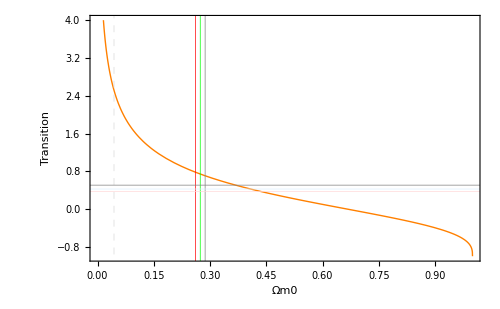

```mathematica
pldecΩm0I2CCPL=Plot[{ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.02,-1.02,0.2],ztr[Ωm0I2CCPL,1-Ωm0I2CCPL]},{Ωm0I2CCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"Q=-0.02 H ρ_d","LCDM"},LegendPosition->{0.0,-0.05},LegendShadow->None,ImageSize->500,FrameLabel->{"Ωm0","Transition"}]
```

```mathematica
plztrI2CCPL[ξI2CCPL_,w0I2CCPL_,w1I2CCPL_,color_,{ranges_:0,rangee_:1}]:=Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{ranges,rangee},{-1,4}},PlotStyle->color,AxesOrigin->{0,-1},Frame->True,FrameLabel->{"Ωm0","Transtion"}];
```

```mathematica
plztrI2CCPLManSum=Manipulate[Show[{plztrI2CCPL[ξI2CCPL,w0I2CCPL,w1I2CCPL,Orange,{0,1}],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],GridLines->{{},{{0,Dashed}}},FrameLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_d, CPL: Transition ~ Ωm0"],{{ξI2CCPL,-0.4,"Interaction"},-1,0,Appearance->"Open"},{{w0I2CCPL,-1.02,"CPL EoS w0"},-2,-0.3,Appearance->"Open"},{{w1I2CCPL,0.6,"CPL EoS w1"},-0.2,1,Appearance->"Open"},Delimiter,Style["Orange is for interacting CPL model with Q=ξ H ρ_m",Medium],ControlPlacement->{Right,Right,Right},SaveDefinitions->True]
```

```mathematica
plztrExamI2CCPLSum=Grid[{{Show[{plztrI2CCPL[-0.1,-1,0.6,Orange,{0,1}],plztrI2CCPL[-0.3,-1,0.6,{Blue,Dashed},{0,1}],plztrI2CCPL[-0.6,-1,0.6,{Green,Dotted},{0,1}],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],GridLines->{{},{{0,Dashed}}},Epilog->Inset[Framed[Style["Orange: w0=-1,w1=0.6,ξ=-0.1\n Blue dashed:w0=-1,w1=0.6,ξ=-0.3\n Green dotted:w0=-1,w1=0.6,ξ=-0.6\n Pink: LCDM",10],Background->LightGreen,FrameStyle->None],{0.3,3.5},{Left,Top}],FrameLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_d, CPL: Transition ~ Ωm0",ImageSize->400],Show[{plztrI2CCPL[-0.3,-1,0.1,Red,{0,1}],plztrI2CCPL[-0.3,-1,0.4,{Purple,Dotted},{0,1}],plztrI2CCPL[-0.3,-1,0.8,{Magenta,Dashed},{0,1}],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],GridLines->{{},{{0,Dashed}}},Epilog->Inset[Framed[Style["Red: w0=-1,w1=0.1,ξ=-0.3\n Magenta dashed:w0=-1,w1=0.8,ξ=-0.3\n Purple dotted:w0=-1,w1=0.4,ξ=-0.3\n Pink: LCDM",10],Background->LightGreen,FrameStyle->None],{0.3,3.5},{Left,Top}],FrameLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_d, CPL: Transition ~ Ωm0",ImageSize->400]}}]
```

-Graphics-

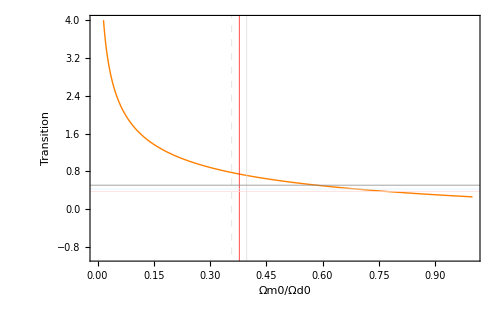

```mathematica
pldecrI2CCPL=Plot[{ztrrI2CCPL[rI2CCPL,-0.6,-1.02,0.6],ztrr[rI2CCPL]},{rI2CCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"CPL,Q=-0.6 H ρ_d","LCDM"},LegendPosition->{0.0,-0.05},LegendShadow->None,ImageSize->500,FrameLabel->{"Ωm0/Ωd0","Transition"}]
```

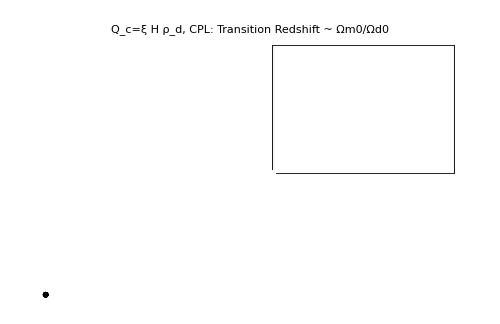

```mathematica
pltransrI2CCPLDense=Show[Table[Plot[{ztrrI2CCPL[rI2CCPL,ξI2CCPL,-1.02,0.6],ztrr[rI2CCPL]},{rI2CCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"CPL,Q=ξ H ρ_d,\n with ξ∈(-0.8,0) step=0.1","LCDM"},LegendPosition->{0.0,-0.05},LegendShadow->None],{ξI2CCPL,-0.8,0,0.1}],ImageSize->500,FrameLabel->{"Ωm0/Ωd0","Transition"},PlotLabel->"Q_c=ξ H ρ_d, CPL: Transition Redshift ~ Ωm0/Ωd0",ImageSize->500]
```

#### Find out allowed region of coupling constant

To find out the region of ξ, set w=-1 and Ωd0=1-Ωm0. Let the ztr-Ωm0 line cross points (0.287,0.508) and (0.261, 0.376).

```mathematica
Off[FindRoot::nlnum]
Off[ReplaceAll::reps]
ztrI2CCPL[Ωm0I2CCPL,Ωd0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]
On[FindRoot::nlnum]
On[ReplaceAll::reps]
```

Re[z/.FindRoot[(1+3 (w0I2CCPL+(w1I2CCPL z)/(1+z))) ΩdI2CCPL[Ωd0I2CCPL,Ωm0I2CCPL,w0I2CCPL,w1I2CCPL,ξI2CCPL,z]+ΩmI2CCPL[Ωm0I2CCPL,ξI2CCPL,z]==0,{z,3}]]

```mathematica
(* ztrICCPL[0.287,1-0.287,ξICCPL1,-1.02,0.6]==0.508 *)
```

```mathematica
ξI2CCPLffunc[Ωm0I2CCPL_,Ωd0I2CCPL_,w0I2CCPL_,w1I2CCPL_,data_]:=ξI2CCPL/.FindRoot[ztrI2CCPL[Ωm0I2CCPL,Ωd0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==data,{ξI2CCPL,-0.6}]
```

```mathematica
ξI2CCPLf2[Ωm0I2CCPL_,Ωd0I2CCPL_,w0I2CCPL_,w1I2CCPL_]:=ξI2CCPL/.FindRoot[ztrI2CCPL[Ωm0I2CCPL,Ωd0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==0.508,{ξI2CCPL,-0.6}]
```

```mathematica
ξI2CCPLf1[Ωm0I2CCPL_,Ωd0I2CCPL_,w0I2CCPL_,w1I2CCPL_]:=ξI2CCPL/.FindRoot[ztrI2CCPL[Ωm0I2CCPL,Ωd0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==0.376,{ξI2CCPL,-0.6}]
```

Cross the Center of best fit. (0.274,0.426)

```mathematica
ξI2CCPLfc[Ωm0I2CCPL_,Ωd0I2CCPL_,w0I2CCPL_,w1I2CCPL_]:=ξI2CCPL/.FindRoot[ztrI2CCPL[Ωm0I2CCPL,Ωd0I2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==0.426,{ξI2CCPL,-0.6}]
```

According to the data of transition redshift.

```mathematica
ξI2CCPLf2[w0I2CCPL_,w1I2CCPL_]:=ξI2CCPLffunc[0.287,1-0.287,w0I2CCPL,w1I2CCPL,0.508]
```

```mathematica
ξI2CCPLf1[w0I2CCPL_,w1I2CCPL_]:=ξI2CCPLffunc[0.261,1-0.261,w0I2CCPL,w1I2CCPL,0.376]
```

```mathematica
ξI2CCPLfc[w0I2CCPL_,w1I2CCPL_]:=ξI2CCPLffunc[0.274,1-0.274,w0I2CCPL,w1I2CCPL,0.426]
```

An example

```mathematica
Off[FindRoot::nlnum]
Off[ReplaceAll::reps]
{ξI2CCPLf1[-1.02,0.6],ξI2CCPLfc[-1.02,0.6],ξI2CCPLf2[-1.02,0.6]}
On[FindRoot::nlnum]
On[ReplaceAll::reps]
```

{ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-1.02,0.6]==0.376,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-1.02,0.6]==0.426,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-1.02,0.6]==0.508,{ξI2CCPL,-0.6}]}

```mathematica
ξI2CCPLrffunc[rI2CCPL_,w0I2CCPL_,w1I2CCPL_,data_]:=ξI2CCPL/.FindRoot[ztrrI2CCPL[rI2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==data,{ξI2CCPL,-0.6}]
```

```mathematica
ξI2CCPLrf2[rI2CCPL_,w0I2CCPL_,w1I2CCPL_]:=ξI2CCPL/.FindRoot[ztrrI2CCPL[rI2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==0.508,{ξI2CCPL,-0.6}]
```

```mathematica
ξI2CCPLrf1[rI2CCPL_,w0I2CCPL_,w1I2CCPL_]:=ξI2CCPL/.FindRoot[ztrrI2CCPL[rI2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==0.376,{ξI2CCPL,-0.6}]
```

Cross the Center of best fit. (0.358,0.426)

```mathematica
ξI2CCPLrfc[rI2CCPL_,w0I2CCPL_,w1I2CCPL_]:=ξI2CCPL/.FindRoot[ztrrI2CCPL[rI2CCPL,ξI2CCPL,w0I2CCPL,w1I2CCPL]==0.426,{ξI2CCPL,-0.6}]
```

According to the data of transition redshift.

```mathematica
ξI2CCPLrf2[w0I2CCPL_,w1I2CCPL_]:=ξI2CCPLrffunc[0.398,w0I2CCPL,w1I2CCPL,0.508]
```

```mathematica
ξI2CCPLrf1[w0I2CCPL_,w1I2CCPL_]:=ξI2CCPLrffunc[0.358,w0I2CCPL,w1I2CCPL,0.376]
```

```mathematica
ξI2CCPLrfc[w0I2CCPL_,w1I2CCPL_]:=ξI2CCPLrffunc[0.378,w0I2CCPL,w1I2CCPL,0.426]
```

An example

```mathematica
Off[FindRoot::nlnum]
Off[ReplaceAll::reps]
{ξI2CCPLrf1[-1.02,0.6],ξI2CCPLrfc[-1.02,0.6],ξI2CCPLrf2[-1.02,0.6]}
On[FindRoot::nlnum]
On[ReplaceAll::reps]
```

{ξI2CCPL/.FindRoot[ztrrI2CCPL[0.358,ξI2CCPL,-1.02,0.6]==0.376,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrrI2CCPL[0.378,ξI2CCPL,-1.02,0.6]==0.426,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrrI2CCPL[0.398,ξI2CCPL,-1.02,0.6]==0.508,{ξI2CCPL,-0.6}]}

```mathematica
Off[FindRoot::nlnum]
Off[ReplaceAll::reps]
fitξI2CCPLManSum=Manipulate[Grid[{{numPlot["(",{ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]},")",{-1.5,1}],Plot[w0I2CCPL+w1I2CCPL temp/(temp+1),{temp,-0.9,10}]}}],{{w0I2CCPL,-1.02,"Equation of State w0"},-2,-0.47,Appearance->"Open"},{{w1I2CCPL,0.6,"Equation of State w1"},-1,1,Appearance->"Open"},Delimiter,Style["This is the fitting result from transition redshift data.",Bold],Delimiter,"The parenthesis shows the upper and lower value \n while the verticle line show the center value.",Style["\n The three numbers are left value, center value, right value respectively."],Delimiter,Delimiter,Style["Slide to see how do the two parameters affect the coupling constant results."],ControlPlacement->{Bottom,Bottom},SaveDefinitions->True]
```

```mathematica
(*
On[FindRoot::nlnum]
On[ReplaceAll::reps]
*)
```

#### Quintom Case

The transition redshift. Six groups of parameters.
(-1, 0.1)  (-1, 0.2)  (-0.9,0.1)
(-1, -0.1)  (-1, -0.2)  (-1.1,-0.1)
In two plots, 
(-1, 0.1)  (-1, 0.2)  (-1, -0.1)  (-1, -0.2) 
(-1, 0.1)   (-0.9,0.1)  (-1, -0.1)   (-1.1,-0.1)

```mathematica
pltI2CCPLEoSfunc[w0I2CCPL_,w1I2CCPL_,color_]:=Plot[{w0I2CCPL+w1I2CCPL z/(1+z)},{z,-0.99,10},PlotStyle->color,AxesLabel->{"z","w"}];
```

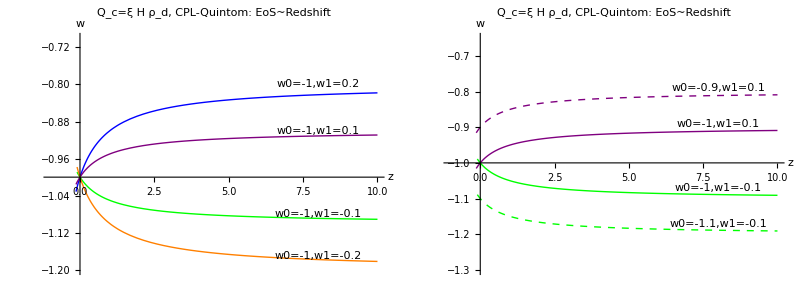

```mathematica
plEoSI2CCPLQuintomSum=Grid[{{Show[pltI2CCPLEoSfunc[-1,0.2,Blue],pltI2CCPLEoSfunc[-1,0.1,Purple],pltI2CCPLEoSfunc[-1,-0.1,Green],pltI2CCPLEoSfunc[-1,-0.2,Orange],PlotRange->{{-0.99,10},{-1.2,-0.7}},AxesOrigin->{0,-1},ImageSize->400,PlotLabel->"Q_c=ξ H ρ_d, CPL-Quintom: EoS~Redshift",Epilog->{Inset[Framed[Style["w0=-1,w1=0.2",10,Blue],Background->None,FrameStyle->None],{8,-0.80},{0,0}],Inset[Framed[Style["w0=-1,w1=0.1",10,Purple],Background->None,FrameStyle->None],{8,-0.9},{0,0}],Inset[Framed[Style["w0=-1,w1=-0.1",10,Green],Background->None,FrameStyle->None],{8,-1.08},{0,0}],Inset[Framed[Style["w0=-1,w1=-0.2",10,Orange],Background->None,FrameStyle->None],{8,-1.17},{0,0}]}],Show[pltI2CCPLEoSfunc[-1,0.1,Purple],pltI2CCPLEoSfunc[-0.9,0.1,{Purple,Dashed}],pltI2CCPLEoSfunc[-1,-0.1,Green],pltI2CCPLEoSfunc[-1.1,-0.1,{Green,Dashed}],PlotRange->{{-1,10},{-1.3,-0.65}},AxesOrigin->{0,-1},ImageSize->400,PlotLabel->"Q_c=ξ H ρ_d, CPL-Quintom: EoS~Redshift",Epilog->{Inset[Framed[Style["w0=-0.9,w1=0.1",10,Purple],Background->None,FrameStyle->None],{8,-0.79},{0,0}],Inset[Framed[Style["w0=-1,w1=0.1",10,Bold,Purple],Background->None,FrameStyle->None],{8,-0.89},{0,0}],Inset[Framed[Style["w0=-1,w1=-0.1",10,Bold,Green],Background->None,FrameStyle->None],{8,-1.07},{0,0}],Inset[Framed[Style["w0=-1.1,w1=-0.1",10,Green],Background->None,FrameStyle->None],{8,-1.17},{0,0}]}]}}]
```

“Purple line:(-1,0.1)─ Blue line: (-1,0.2) Green line:(-1,-0.1)\n─ Pink line:LCDM”
“Purple Dashed:(-0.9,0.1)  Green Dashed:(-1.1,0.1)”

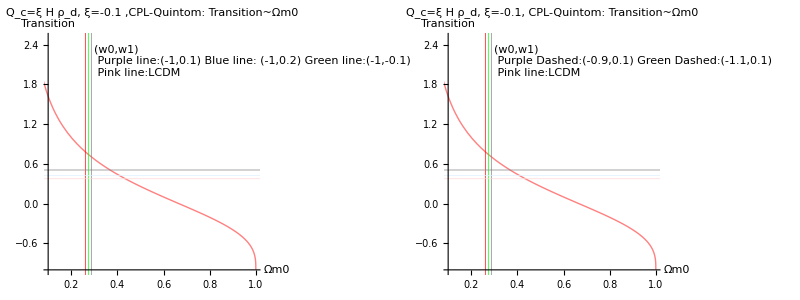

```mathematica
plztrI2CCPLQuintomSum=Grid[{{Show[{plztrI2CCPL[-0.1,-1,0.1,Purple,{0.1,1}],plztrI2CCPL[-0.1,-1,0.2,Blue,{0.1,1}],plztrI2CCPL[-0.1,-1,-0.1,Green,{0.1,1}],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0.1,1},{-1,3}},PlotStyle->Pink,AxesOrigin->{0.1,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.1,-1},PlotRange->{{0.1,1},{-1,2.5}},Frame->False,AxesLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_d, ξ=-0.1 ,CPL-Quintom: Transition~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple line:(-1,0.1) Blue line: (-1,0.2) Green line:(-1,-0.1)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.3,2.4},{Left,Top}],ImageSize->400],Show[{plztrI2CCPL[-0.1,-1,0.1,Purple,{0.1,1}],plztrI2CCPL[-0.1,-0.9,0.1,{Purple,Dashed},{0.1,1}],plztrI2CCPL[-0.1,-1,-0.1,Green,{0.1,1}],plztrI2CCPL[-0.1,-1.1,-0.1,{Green,Dashed},{0.1,1}],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0.1,1},{-1,3}},PlotStyle->Pink,AxesOrigin->{0.1,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.1,-1},PlotRange->{{0.1,1},{-1,2.5}},Frame->False,AxesLabel->{"Ωm0","Transition"},PlotLabel->"Q_c=ξ H ρ_d, ξ=-0.1, CPL-Quintom: Transition~Ωm0",Epilog->Inset[Framed[Style["(w0,w1)\n Purple Dashed:(-0.9,0.1) Green Dashed:(-1.1,0.1)\n Pink line:LCDM",10],Background->None,FrameStyle->None],{0.3,2.4},{Left,Top}],ImageSize->400]}}]//Quiet
```

As for the effect of EoS, we can split it to w0 effect and w1 effect.

First construct the plot function.

```mathematica
(*
pltξvw0I2CCPL[w1I2CCPL_,w0I2CCPLs_,w0I2CCPLe_]:=Plot[{ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]},{w0I2CCPL,w0I2CCPLs,w0I2CCPLe}]
*)
```

Choose the values from Reference 3. w0 = -1.087 ± 0.096,

```mathematica
ξvwExamI2CCPLQuintom={Block[{w0I2CCPL=-1,w1I2CCPL=-0.1},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-1,w1I2CCPL=0},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-1,w1I2CCPL=0.1},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-0.9,w1I2CCPL=0.1},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-1.1,w1I2CCPL=-0.1},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}]}
```

{{{-1,-0.1},ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-1,-0.1]==0.426,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-1,-0.1]==0.376,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-1,-0.1]==0.508,{ξI2CCPL,-0.6}]},{{-1,0},ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-1,0]==0.426,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-1,0]==0.376,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-1,0]==0.508,{ξI2CCPL,-0.6}]},{{-1,0.1},ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-1,0.1]==0.426,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-1,0.1]==0.376,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-1,0.1]==0.508,{ξI2CCPL,-0.6}]},{{-0.9,0.1},ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-0.9,0.1]==0.426,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-0.9,0.1]==0.376,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-0.9,0.1]==0.508,{ξI2CCPL,-0.6}]},{{-1.1,-0.1},ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-1.1,-0.1]==0.426,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-1.1,-0.1]==0.376,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-1.1,-0.1]==0.508,{ξI2CCPL,-0.6}]}}

```mathematica
tabξvwExamI2CCPLQuintom=Grid[Prepend[Prepend[ξvwExamI2CCPLQuintom,{"{w0,w1}","Center","Lower","Upper"}],{"ξ results for Q_c=ξ H ρ_d, CPL,Quintom.",SpanFromLeft}],Frame->All,Background->{{LightGray,None},{LightGreen,LightGray,None}},Alignment->Center,ItemSize->8]
```

ξ results for Q_c=ξ H ρ_d, CPL,Quintom. |  |  | 
{w0,w1} | Center | Lower | Upper
{-1,-0.1} | ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-1,-0.1]==0.426,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-1,-0.1]==0.376,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-1,-0.1]==0.508,{ξI2CCPL,-0.6}]
{-1,0} | ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-1,0]==0.426,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-1,0]==0.376,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-1,0]==0.508,{ξI2CCPL,-0.6}]
{-1,0.1} | ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-1,0.1]==0.426,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-1,0.1]==0.376,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-1,0.1]==0.508,{ξI2CCPL,-0.6}]
{-0.9,0.1} | ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-0.9,0.1]==0.426,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-0.9,0.1]==0.376,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-0.9,0.1]==0.508,{ξI2CCPL,-0.6}]
{-1.1,-0.1} | ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-1.1,-0.1]==0.426,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-1.1,-0.1]==0.376,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-1.1,-0.1]==0.508,{ξI2CCPL,-0.6}]

```mathematica
(*
pltξvwExamI2CCPL=Show[pltξvwI2CCPL[????????],GridLines→{{{ξvwExamICC[[1,1]],Directive[Gray,Dashed]},{ξvwExamICC[[2,1]],Directive[Gray,Dotted]},{ξvwExamICC[[3,1]],Directive[Gray,DotDashed]}},{{ξvwExamICC[[1,3]],Directive[Orange,Dashed]},{ξvwExamICC[[1,2]],Directive[Blue,Dashed]},{ξvwExamICC[[1,4]],Directive[Red,Dashed]},{ξvwExamICC[[2,3]],Directive[Orange,Dotted]},{ξvwExamICC[[2,2]],Directive[Blue,Dotted]},{ξvwExamICC[[2,4]],Directive[Red,Dotted]},{ξvwExamICC[[3,3]],Directive[Orange,DotDashed]},{ξvwExamICC[[3,2]],Directive[Blue,DotDashed]},{ξvwExamICC[[3,4]],Directive[Red,DotDashed]}}},Epilog→{Inset[Framed[Style["w = -1.087 ± 0.096",10],Background→LightBlue,FrameStyle→None],{-1.087,0.8},{0,Top}],Inset[Framed[Style["Orange:Ωm0=0.261;Transition=0.376\n Blue:Ωm0=0.274;Transition=0.426\n Red:Ωm0=0.287;Transition=0.508",11],Background→LightGreen,FrameStyle→None],{-1.95,0.84},{Left,Top}]},ImageSize→500]
*)
```

```mathematica
pltfitξI2CCPLfunc[w0I2CCPL_,w1I2CCPL_]:=Grid[{{numPlot["(",{ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]},")",{-2,1}]},{Plot[w0I2CCPL+w1I2CCPL temp/(temp+1),{temp,-0.9,10},Epilog->Inset[Framed[Style[{w0I2CCPL,w1I2CCPL},10],Background->LightYellow],{Center,Center},{Center,Center}]]}}];
```

```mathematica
pltfitξI2CCPLQuintomSum=Grid[{{pltfitξI2CCPLfunc[-1,0.1],pltfitξI2CCPLfunc[-1,0.2],pltfitξI2CCPLfunc[-1,-0.1]},{pltfitξI2CCPLfunc[-0.9,0.1],pltfitξI2CCPLfunc[-1.1,-0.1]}}]
```

-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-
-Graphics-
-Graphics- | -Graphics-
-Graphics- |

#### Quintessence

Choose some Quintessence parameters.
(-0.9,-0.05) (-0.8,-0.05)(-0.8,-0.1)

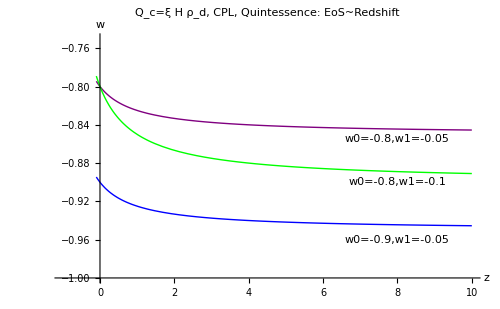

```mathematica
plEoSI2CCPLQuintessenceSum=Grid[{{Show[pltI2CCPLEoSfunc[-0.9,-0.05,Blue],pltI2CCPLEoSfunc[-0.8,-0.05,Purple],pltI2CCPLEoSfunc[-0.8,-0.1,Green],PlotRange->{{-0.99,10},{-1.0,-0.75}},AxesOrigin->{0,-1},Epilog->{Inset[Framed[Style["w0=-0.9,w1=-0.05",10,Blue],Background->None,FrameStyle->None],{8,-0.96},{0,0}],Inset[Framed[Style["w0=-0.8,w1=-0.05",10,Purple],Background->None,FrameStyle->None],{8,-0.855},{0,0}],Inset[Framed[Style["w0=-0.8,w1=-0.1",10,Green],Background->None,FrameStyle->None],{8,-0.9},{0,0}]},PlotLabel->"Q_c=ξ H ρ_d, CPL, Quintessence: EoS~Redshift",ImageSize->500]}}]
```

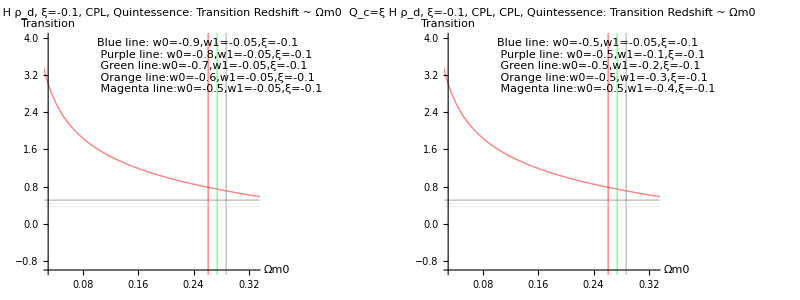

```mathematica
plztrI2CCPLQuintessenceSum=Grid[{{Show[{Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.9,-0.05],{Ωm0I2CCPL,0.01,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Blue,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.8,-0.05],{Ωm0I2CCPL,0.01,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Purple,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.7,-0.05],{Ωm0I2CCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Green,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.6,-0.05],{Ωm0I2CCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Orange,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.5,-0.05],{Ωm0I2CCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Magenta,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0.01,0.94},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.03,-1},PlotRange->{{0.03,0.33},Automatic},Frame->False,AxesLabel->{"Ωm0","Transition"},Epilog->Inset[Framed[Style["Blue line: w0=-0.9,w1=-0.05,ξ=-0.1\n Purple line: w0=-0.8,w1=-0.05,ξ=-0.1\n Green line:w0=-0.7,w1=-0.05,ξ=-0.1\n Orange line:w0=-0.6,w1=-0.05,ξ=-0.1\n Magenta line:w0=-0.5,w1=-0.05,ξ=-0.1",10],Background->LightGreen,FrameStyle->None],{0.1,4},{Left,Top}],PlotLabel->"Q_c=ξ H ρ_d, ξ=-0.1, CPL, Quintessence: Transition Redshift ~ Ωm0",ImageSize->400],Show[{Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.5,-0.05],{Ωm0I2CCPL,0.01,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Blue,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.5,-0.1],{Ωm0I2CCPL,0.01,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Purple,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.5,-0.2],{Ωm0I2CCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Green,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.5,-0.3],{Ωm0I2CCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Orange,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztrI2CCPL[Ωm0I2CCPL,1-Ωm0I2CCPL,-0.1,-0.5,-0.4],{Ωm0I2CCPL,0.01,0.94},PlotRange->{{0,1},{-1,4}},PlotStyle->Magenta,AxesOrigin->{0,-1},PerformanceGoal->"Quality"],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0.01,0.94},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},GridLines->{{{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},AxesOrigin->{0.03,-1},PlotRange->{{0.03,0.33},Automatic},Frame->False,AxesLabel->{"Ωm0","Transition"},Epilog->Inset[Framed[Style["Blue line: w0=-0.5,w1=-0.05,ξ=-0.1\n Purple line: w0=-0.5,w1=-0.1,ξ=-0.1\n Green line:w0=-0.5,w1=-0.2,ξ=-0.1\n Orange line:w0=-0.5,w1=-0.3,ξ=-0.1\n Magenta line:w0=-0.5,w1=-0.4,ξ=-0.1",10],Background->LightGreen,FrameStyle->None],{0.1,4},{Left,Top}],PlotLabel->"Q_c=ξ H ρ_d, ξ=-0.1, CPL, CPL, Quintessence: Transition Redshift ~ Ωm0",ImageSize->400]}}]
```

As for the effect of EoS, we can split it to w0 effect and w1 effect.

Choose some values of w0 and w1 causually.

```mathematica
ξvwExamI2CCPLQuintessence={Block[{w0I2CCPL=-0.9,w1I2CCPL=-0.05},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-0.8,w1I2CCPL=-0.05},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-0.8,w1I2CCPL=-0.1},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}]}
```

{{{-0.9,-0.05},ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-0.9,-0.05]==0.426,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-0.9,-0.05]==0.376,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-0.9,-0.05]==0.508,{ξI2CCPL,-0.6}]},{{-0.8,-0.05},ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-0.8,-0.05]==0.426,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-0.8,-0.05]==0.376,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-0.8,-0.05]==0.508,{ξI2CCPL,-0.6}]},{{-0.8,-0.1},ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-0.8,-0.1]==0.426,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-0.8,-0.1]==0.376,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-0.8,-0.1]==0.508,{ξI2CCPL,-0.6}]}}

```mathematica
tabξvwExamI2CCPLQuintessence=Grid[Prepend[Prepend[ξvwExamI2CCPLQuintessence,{"{w0,w1}","Center","Lower","Upper"}],{"ξ results for Q_c=ξ H ρ_d, CPL,Quintessence.",SpanFromLeft}],Frame->All,Background->{{LightGray,None},{LightGreen,LightGray,None}},Alignment->Center,ItemSize->8]
```

ξ results for Q_c=ξ H ρ_d, CPL,Quintessence. |  |  | 
{w0,w1} | Center | Lower | Upper
{-0.9,-0.05} | ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-0.9,-0.05]==0.426,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-0.9,-0.05]==0.376,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-0.9,-0.05]==0.508,{ξI2CCPL,-0.6}]
{-0.8,-0.05} | ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-0.8,-0.05]==0.426,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-0.8,-0.05]==0.376,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-0.8,-0.05]==0.508,{ξI2CCPL,-0.6}]
{-0.8,-0.1} | ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-0.8,-0.1]==0.426,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-0.8,-0.1]==0.376,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-0.8,-0.1]==0.508,{ξI2CCPL,-0.6}]

```mathematica
pltfitξI2CCPLQuintessenceSum=Grid[{{pltfitξI2CCPLfunc[-0.9,-0.05],pltfitξI2CCPLfunc[-0.8,-0.05],pltfitξI2CCPLfunc[-0.8,-0.1]}}]
```

-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-

#### Phantom

Some parameters that give us a phantom mode
(-1.1,0.05) (-1.2,0.05) (-1.2,0.1)

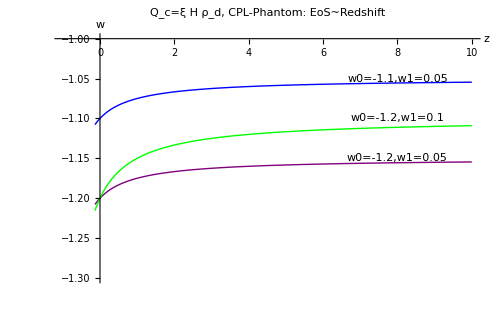

```mathematica
plEoSI2CCPLPhantomSum=Grid[{{Show[pltI2CCPLEoSfunc[-1.1,0.05,Blue],pltI2CCPLEoSfunc[-1.2,0.05,Purple],pltI2CCPLEoSfunc[-1.2,0.1,Green],PlotRange->{{-0.99,10},{-1.3,-1}},AxesOrigin->{0,-1},Epilog->{Inset[Framed[Style["w0=-1.1,w1=0.05",10,Blue],Background->None,FrameStyle->None],{8,-1.05},{0,0}],Inset[Framed[Style["w0=-1.2,w1=0.05",10,Purple],Background->None,FrameStyle->None],{8,-1.15},{0,0}],Inset[Framed[Style["w0=-1.2,w1=0.1",10,Green],Background->None,FrameStyle->None],{8,-1.1},{0,0}]},PlotLabel->"Q_c=ξ H ρ_d, CPL-Phantom: EoS~Redshift",ImageSize->500]}}]
```

```mathematica
plztrI2CCPLPhantomSum=Grid[{{Show[{plztrI2CCPL[-0.1,-1.1,0.05,Blue,{0,1}],plztrI2CCPL[-0.1,-1.2,0.05,Purple,{0,1}],plztrI2CCPL[-0.1,-1.2,0.1,Green,{0,1}],Plot[ztr[Ωm0I2CCPL,1-Ωm0I2CCPL],{Ωm0I2CCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.261,.2752}],Scaled[{0.287,.3016}]]},Frame->True],AxesOrigin->{0,-1},Frame->False,AxesLabel->{"Ωm0","Transition"},Epilog->Inset[Framed[Style["Blue line: w0=-1.1,w1=0.05,ξ=-0.1\n Purple line: w0=-1.2,w1=0.05,ξ=-0.1\n Green line:w0=-1.2,w1=0.1,ξ=-0.1",10],Background->LightGreen,FrameStyle->None],{0.35,3.5},{0,0}],PlotLabel->"Q_c=ξ H ρ_d, CPL-Phantom: Transition ~ Ωm0",ImageSize->500]}}]
```

-Graphics-

As for the effect of EoS, we can split it to w0 effect and w1 effect.

Choose some values of w0 and w1 causually.

```mathematica
ξvwExamI2CCPLPhantom={Block[{w0I2CCPL=-1.1,w1I2CCPL=0.05},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-1.2,w1I2CCPL=0.05},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}],Block[{w0I2CCPL=-1.2,w1I2CCPL=0.1},{{w0I2CCPL,w1I2CCPL},ξI2CCPLfc[w0I2CCPL,w1I2CCPL],ξI2CCPLf1[w0I2CCPL,w1I2CCPL],ξI2CCPLf2[w0I2CCPL,w1I2CCPL]}]}
```

{{{-1.1,0.05},ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-1.1,0.05]==0.426,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-1.1,0.05]==0.376,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-1.1,0.05]==0.508,{ξI2CCPL,-0.6}]},{{-1.2,0.05},ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-1.2,0.05]==0.426,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-1.2,0.05]==0.376,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-1.2,0.05]==0.508,{ξI2CCPL,-0.6}]},{{-1.2,0.1},ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-1.2,0.1]==0.426,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-1.2,0.1]==0.376,{ξI2CCPL,-0.6}],ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-1.2,0.1]==0.508,{ξI2CCPL,-0.6}]}}

```mathematica
tabξvwExamI2CCPLPhantom=Grid[Prepend[Prepend[ξvwExamI2CCPLPhantom,{"{w0,w1}","Center","Lower","Upper"}],{"ξ results for Q_c=ξ H ρ_d, CPL,Phantom.",SpanFromLeft}],Frame->All,Background->{{LightGray,None},{LightGreen,LightGray,None}},Alignment->Center,ItemSize->8]
```

ξ results for Q_c=ξ H ρ_d, CPL,Phantom. |  |  | 
{w0,w1} | Center | Lower | Upper
{-1.1,0.05} | ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-1.1,0.05]==0.426,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-1.1,0.05]==0.376,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-1.1,0.05]==0.508,{ξI2CCPL,-0.6}]
{-1.2,0.05} | ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-1.2,0.05]==0.426,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-1.2,0.05]==0.376,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-1.2,0.05]==0.508,{ξI2CCPL,-0.6}]
{-1.2,0.1} | ξI2CCPL/.FindRoot[ztrI2CCPL[0.274,0.726,ξI2CCPL,-1.2,0.1]==0.426,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.261,0.739,ξI2CCPL,-1.2,0.1]==0.376,{ξI2CCPL,-0.6}] | ξI2CCPL/.FindRoot[ztrI2CCPL[0.287,0.713,ξI2CCPL,-1.2,0.1]==0.508,{ξI2CCPL,-0.6}]

```mathematica
pltfitξI2CCPLPhantomSum=Grid[{{pltfitξI2CCPLfunc[-1.1,0.05],pltfitξI2CCPLfunc[-1.2,0.05],pltfitξI2CCPLfunc[-1.2,0.1]}}]
```

-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-

## Summary

### Interacting models

#### List of what to make clear

[Quantitively] Fixed Ωm0, the allowed ξ with a changing of EoS.

[Quantitively] Fixed ω, the allowed ξ with a change Ωm0 or r.

[Quantitively] ξ is minus means energy transfer to dark matter, which delays the appearence of dark energy dominated era. What is the result of this method.

[Quantitively] CPL parameterization can be categorized into 3 cases. Check their effects on the fitting. How do different category change the ξ fitting results.

Phantom

Quintessence

Crossing -1, Quintom

[Quantitively] The effect of Ωm0 in different CPL parameterizations.

#### BASIC

Evolution of energy density for Q_c=ξ H ρ_c, constant ξ, constant w, and ξ≠-3w

Ωm=Ωm0 (1+z)^(3-ξ)

Ωd=(Ωd0+ξ/(3w+ξ)Ωm0)(1+z)^(3(1+w))+-ξ/(3w+ξ)Ωm≡Ωd0'(1+z)^(3(1+w))+-ξ/(3w+ξ)Ωm

Evolution of energy density for Q_c=ξ H ρ_d, constant ξ, constant w, and ξ≠-3w

Ωm=(Ωm0+ξ/(ξ+3w)Ωd0)(1+z)^3+-ξ/(ξ+3w)Ωd≡Ωm0'(1+z)^3+-ξ/(ξ+3w)Ωd

Ωd=Ωd0(1+z)^(3(1+w)+ξ)

So in the two cases, coupling constant has two effects:

Amplifies the curve of deceleration parameter.

Energy flow between DE and DM.

### Interacting model Q_c=ξ H ρ_c with constant ξ and constant EoS w.

Derived from (transition redshift, Ωm0) plane, the allowed region for coupling constant ξ is  (-1.28, -0.46) with a center at -0.88, i.e., -0.88_-0.40^(+0.42),  taken the case that the universe is flat, and choose the EoS parameter {w=-1}.
Derived from the (transition redshift, Ωm0/Ωd0) plane, the allowed region of coupling constant ξ is  (-1.25,- 0.47) with a center at -0.88, i.e., -0.88_-0.37^(+0.41) .
There is a bit difference between the two answers. One possible reason is the second method doesn’t assume a flat universe, while the first one supposes the universe is flat.

The full table of fitting results are shown below. The light purple element are the final resuls.

```mathematica
tabξFinaltICC
```

Q_c=ξ H ρ_c, constant ξ, constant w=-1: Results for ξ |  |  | 
Ωm0/Ωd0⋱Transition | z_t=0.376 | z_t=0.426 | z_t=0.508
r=0.358 | -1.25282 | -0.965436 | -0.617444
r=0.378 | -1.15011 | -0.875189 | -0.542347
r=0.398 | -1.05453 | -0.791252 | -0.472561

To check the consistancy of the two methods ( (Transition, Ωm0) plane fitting and (Transition, Ωm0/Ωd0) plane fitting ), we find out the fitting results of coupling constant ξ for a flat universe, i.e., r=Ωm0/(1-Ωm0) in the (Transition, Ωm0) plane, applying the data from (Transition, Ωm0/Ωd0) plane. 
By solving out Ωm0, we get Ωm0=r/(1+r)(this is a monotonic function) in this case. Thus if we use the constrain that r∈(0.358, 0.398) with a center value 0.378, the value of Ωm0 is (0.263623,0.284692), centered at 0.274311. Use this set of value of Ωm0 as the contrain, we have the fitting results in (Transition, Ωm0) plane, which is -0.88_-0.37^(+0.41). This result is exactly the same as the result directly derived from (transition redshift, Ωm0/Ωd0) plane. The same has been done to Q_c=ξ H ρ_d with ξ constant and w constant model, and the result is that the two methods are also consistant.

The plots of deceleration parameter are shown below. At the limit z->Infinity, the deceleration parameter is degenerate for different Ωm0 in this constant ξ and constant w model. 
Theoretically, this limit is determined by the interaction coupling constant ξ, which is (1-ξ)/2, with 3w+ξ<0.

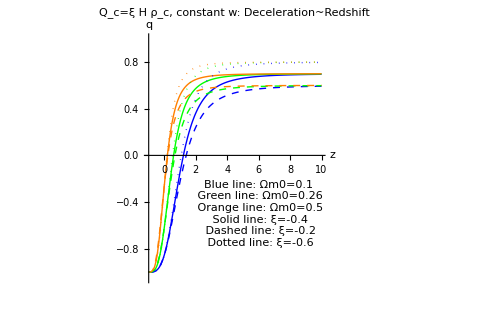

```mathematica
pldecICCShowSum
```

Check the effect of different parameters on deceleration parameter. 
Interaction ξ changes the value of deceleration parameter at z→ ∞ limit. EoS changes the the whole shape. Matter fraction determines how fast q varies, but just in a small time scale.

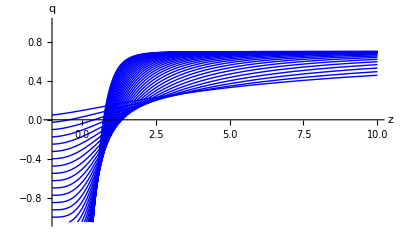
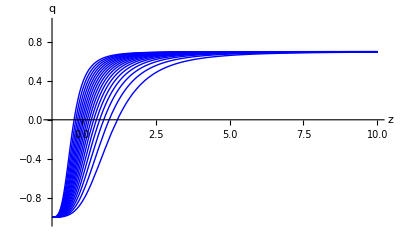
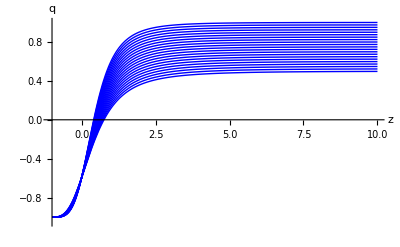
Q_c=ξ H ρ_c with constant ξ and w |  | 
Varying EoS | Varying Ωm0 | Varying ξ
-Graphics- | -Graphics- | -Graphics-

```mathematica
varyingICCShowSum
```

A toy to play with is also provied. Slide the bars to view the effects of different parameters on deceleration parameter.

```mathematica
pldecICCManSum
```

It can be inferred from the expression for Ωm and Ωd that if the transition happens before z=0, increasing couling ξ will bring forward the transition and if the it happens after z=0, increasing coupling ξ will delay the emergence of transition. The following figure shows this result.
Gray rectangle is the region given by Riess (References, Data From, 2).

Orange for w=-1
Blue for w=-0.9

Solid line: ξ=0.2
Dashed line: ξ=0.1
Dotted line: ξ=-0.1
DotDashed line: ξ=-0.2

Pink solid line:w=-1, ξ=0

```mathematica
plztrvsΩm0ICCSum
```

-Graphics-

This can also be seen clearly from the following toy. Gray rectangle is the region given by Riess (References, Data From, 2) .

```mathematica
plztrICCManSum
```

The fitting results of coupling constant ξ can also be dynamic.

```mathematica
fitξICCManSum
```

For different constant EoS, the fitting results using Ωm0∈(0.261,0.287) with a center value 0.274 and Transition redshift ∈ (0.376,0.508) with a center value 0.426. When EoS is very small, the line cross zero. But that is not so useful.

Some data points are derived using w = -1.087 ± 0.096 (from Reference, Data From, 3).

```mathematica
tabξvwExamICC
```

ξ results for Q_c=ξ H ρ_c (Fitting data: Data From, 2) |  |  | 
w | Center | Lower | Upper
-1.183 | -0.881565 | -1.29687 | -0.443589
-1.087 | -0.88948 | -1.29859 | -0.459135
-0.991 | -0.875238 | -1.27522 | -0.456176

A plot showing these data points and the curves of ξ ~ w.

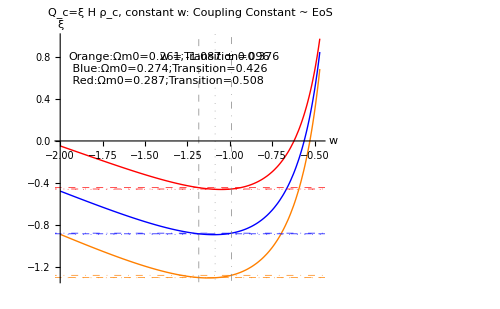

```mathematica
pltξvwExamICC
```

Or just casually use the following parameters.
( -1 within 5%: (-1.05,-0.95))
w=-1  (-1.279,-0.457) center:-0.878
w=-1.05  (-1.293,-0.461) center:-0.887
w=-0.95  (-1.255,-0.447) center:-0.860

The following graph show how do ξ changes with EoS. The grid lines are the results of w=-1±0.05. Two verticle lines are -1.05 and -0.95 respectively. Horizontal lines are their intersections with the ξ~w lines.

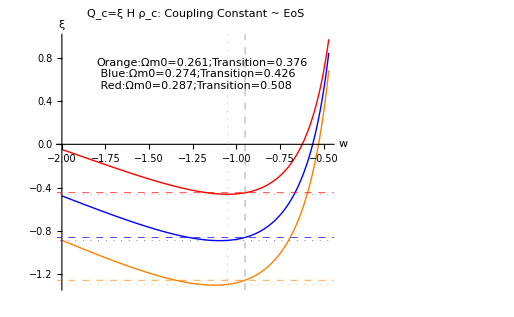

```mathematica
pltξvwExam1ICC
```

Now we assume we do not have the observed Ωm0 data, how do this Ωm0 change the result of ξ. In other words, if the observed Ωm0 data float around some value, then how is the fitting result? We also consider the curvature.
In the figure below, it seems that there is a point where three lines converge. This has something to do with the phenomena that

```mathematica
pltξvΩm0ICCManSum
```

Some data for flat ΛCDM universe. The following data shows how Ωm0 change our results for ξ if we already have transition redshift data {0.426|0.376,0.508}.

If Ωm0 varies 5 percent from 0.274,

```mathematica
tabξICCSum
```

For Ωm0∈0.274 (1±0.05) Table of ξ for different Ωm0~Transition combination |  |  | 
Ωm0Transition | 0.426 | 0.376 | 0.508
0.2603 | -0.994339 | -1.28571 | -0.641508
0.274 | -0.877755 | -1.15303 | -0.544482
0.2877 | -0.767582 | -1.02756 | -0.452892

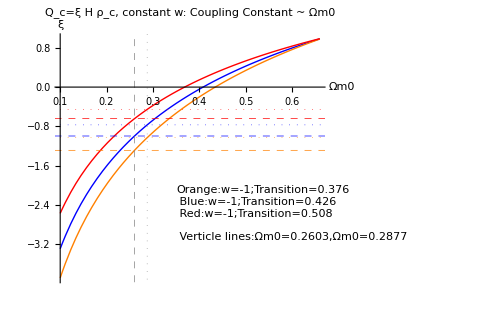

```mathematica
pltξvΩm0ICCSum
```

Besides Ωm0, we can also find out the effects of Curvature, EoS. Assuming we have a constrain of Transition redshift (0.376,0.508) with a center at 0.426.

```mathematica
fitξ2ICCManSum
```

### Interacting model Q_c=ξ H ρ_c with constant ξ and CPL parameterized EoS w=w0+w1 z/(1+z).

For a flat universe, choose the parameters {w0=-1.02,w1=0.6}, the region for interation cosntant ξ should be  (-1.04,-0.21) with a center at -0.64, i.e., -0.64_-0.40^(+0.42) ,derived from the (transition redshift, Ωm0) plane, while a result of (-1.01, -0.23) with a center at -0.63, i.e., -0.63_-0.38^(+0.40) , derived from (transition redshift, Ωm0/Ωd0) plane.

Deceleration parameter is shown below. Behaves similiar to the constant ξ constant w situation.

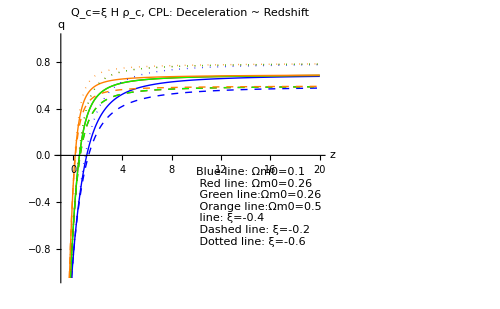

```mathematica
pldecICCPLShowSum
```

The following plots shows the effect of different parameters. Each plot shows how do the deceleration parameter vs redshift line change under  uniformly distributed w0,w1,Ωm0 or ξ.
w0 moves the line up or down, but not monotonously;
w1 changes the late time behavior;
Ωm0 changes the slope;
ξ has moves the line up or down;

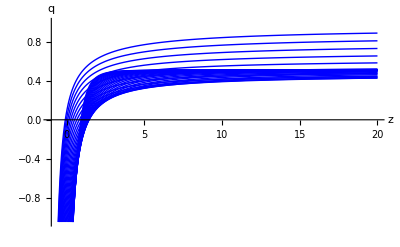
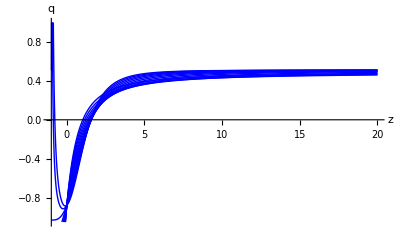
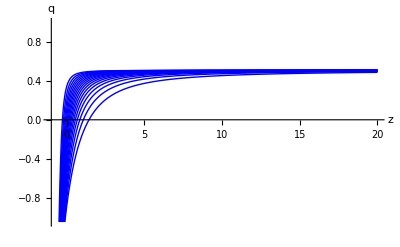
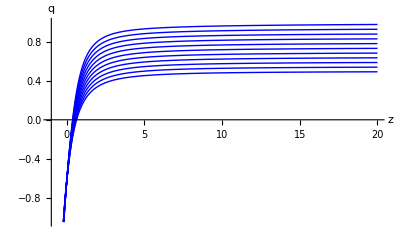
Q_c=ξ H ρ_c, CPL |  |  | 
Varying CPL w0 | Varying CPL w1 | Varying Ωm0 | Varying ξ
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
varyingICCPLShowSum
```

A toy to play with the q~z plot. When ξ=0, w0=-1, w1=0, the curve reduced to LCDM curve.

```mathematica
pldecICCPLManSum
```

A plot shows how bad it is to use transition redshift to constrain interacting model. This is a CPL parameterized example. For ξ∈(-0.8,0), the line just stays near the allowed region constrained by Riess’s results (References, Data From, 2).

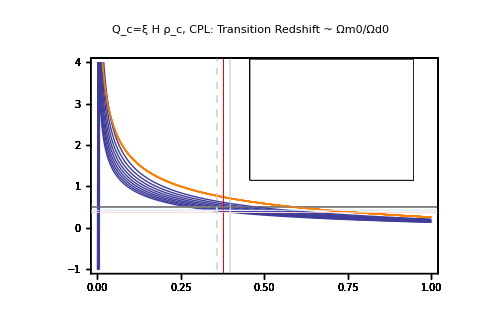

```mathematica
pltransrICCPLDense
```

From the manipulate below, we find for w0=-1, there is a point on this transition ~ Ωm0 curve do not change with coupling constant ξ and w1. (Well, what’s the use of that... )

```mathematica
plztrICCPLManSum
```

An explicit proof of this statement.

```mathematica
plztrExamICCPLSum
```

-Graphics-

A manipulate of the fitting results.

```mathematica
fitξICCPLManSum
```

#### Category

For different w0 and w1 in its EoS equation,

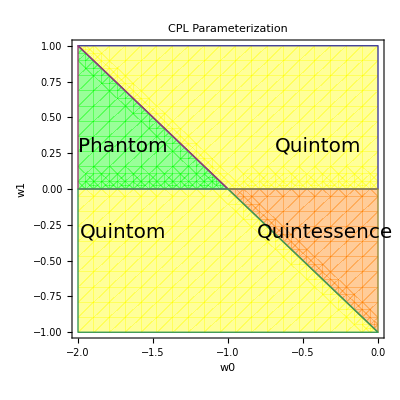

```mathematica
plEoSPhaseICCPL
```

#### Quintom

Color illustrations for the following two figures.
“Purple line:(-1,0.1)─ Blue line: (-1,0.2) Green line:(-1,-0.1)\n─ Pink line:LCDM”
“Purple Dashed:(-0.9,0.1)  Green Dashed:(-1.1,0.1)”

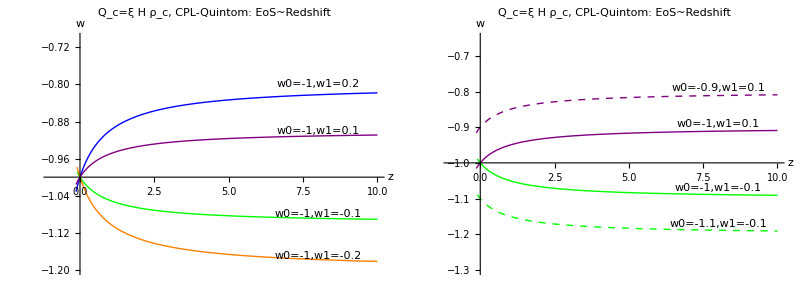

```mathematica
plEoSICCPLQuintomSum
```

Plots of Transition redshift vs Ωm0.
Legends are shown on the plots. Hard to distingush from each other.

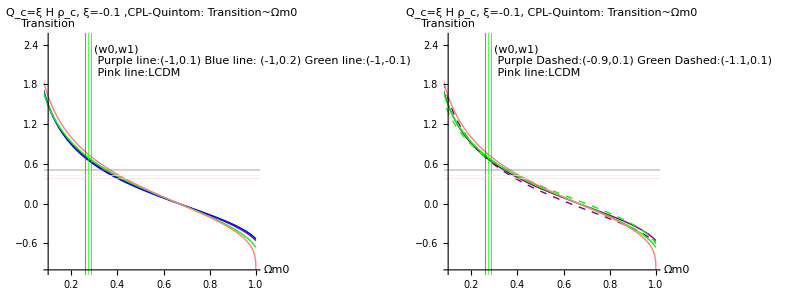

```mathematica
plztrICCPLQuintomSum
```

For different EoS, the fitting results are different. The following table and plots show how do w0 and w1 change the results.

```mathematica
tabξvwExamICCPLQuintom
```

ξ results for Q_c=ξ H ρ_d, CPL,Quintom. |  |  | 
{w0,w1} | Center | Lower | Upper
{-1,-0.1} | -0.907284 | -1.3096 | -0.484861
{-1,0} | -0.877755 | -1.27874 | -0.457448
{-1,0.1} | -0.844859 | -1.24477 | -0.426298
{-0.9,0.1} | -0.785036 | -1.17144 | -0.383258
{-1.1,-0.1} | -0.910565 | -1.3218 | -0.477189

```mathematica
pltfitξICCPLQuintomSum
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

#### Quintessence

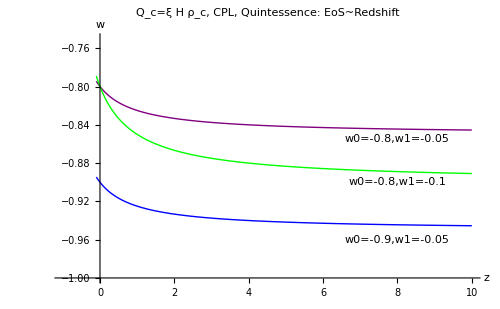

```mathematica
plEoSICCPLQuintessenceSum
```

Different from constant w results,

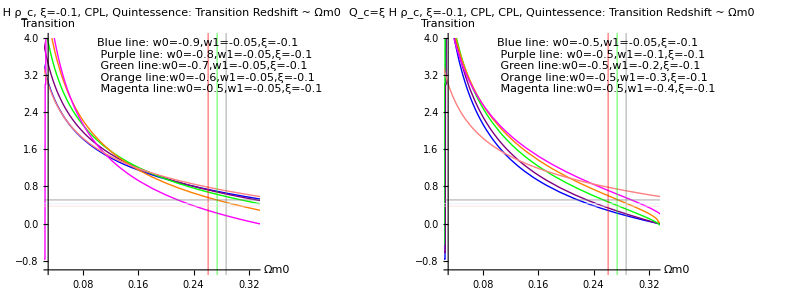

```mathematica
plztrICCPLQuintessenceSum
```

Some ξ fitting results are shown below. This shows how do w0 and w1 change ξ results.

```mathematica
tabξvwExamICCPLQuintessence
```

ξ results for Q_c=ξ H ρ_d, CPL,Quintessence. |  |  | 
{w0,w1} | Center | Lower | Upper
{-0.9,-0.05} | -0.853591 | -1.24197 | -0.448612
{-0.8,-0.05} | -0.765204 | -1.1341 | -0.384235
{-0.8,-0.1} | -0.794865 | -1.16484 | -0.412217

```mathematica
pltfitξICCPLQuintessenceSum
```

-Graphics- | -Graphics- | -Graphics-

#### Phantom

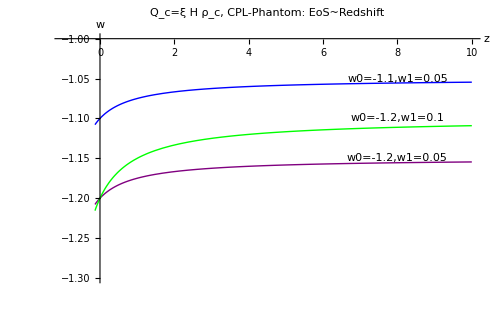

```mathematica
plEoSICCPLPhantomSum
```

```mathematica
plztrICCPLPhantomSum
```

-Graphics-

```mathematica
tabξvwExamICCPLPhantom
```

ξ results for Q_c=ξ H ρ_d, CPL,Phantom. |  |  | 
{w0,w1} | Center | Lower | Upper
{-1.1,0.05} | -0.878139 | -1.28773 | -0.447379
{-1.2,0.05} | -0.870255 | -1.28596 | -0.431951
{-1.2,0.1} | -0.861665 | -1.27697 | -0.424022

```mathematica
pltfitξICCPLPhantomSum
```

-Graphics- | -Graphics- | -Graphics-

### Interacting model Q_c=ξ H ρ_d with constant ξ and constant EoS w.

Derived from (transition redshift, Ωm0) plane, the allowed region for coupling constant ξ is ( -1.06,-0.42) with a center at -0.76, i.e., -0.76_-0.30^(+0.34) ,  taken the case that the universe is flat, and choose the EoS parameter {w=-1}.
Derived from the (transition redshift, Ωm0/Ωd0) plane, the allowed region of coupling constant ξ is (-1.07,-0.41) with a center at -0.76, i.e., -0.76_-0.31^(+0.35).

The plots of deceleration parameter are shown below. At the limit z->Infinity, the deceleration parameter ALL goes to 1/2.
Theoretically, this limit is  1/2 which is not related to any parameters, with 3w+ξ<0.

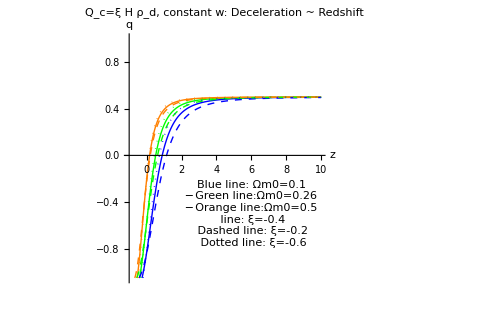

```mathematica
pldecI2CCShowSum
```

To check the effect of different parameters, another plot is shown.

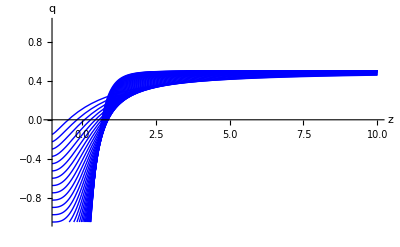
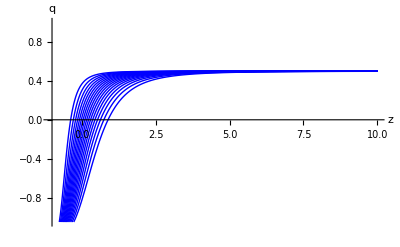
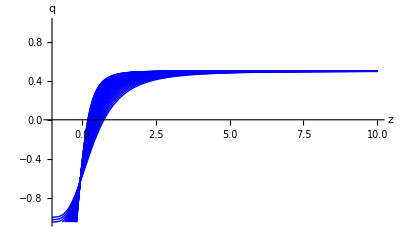
Varying EoS | Varying Ωm0 | Varying ξ
-Graphics- | -Graphics- | -Graphics-

```mathematica
varyingI2CCShowSum
```

A toy to play with deceleration vs z curve is also provied

```mathematica
pldecI2CCManSum
```

If the transition happens before z=0, increasing couling ξ will delay the transition.
If the it happens after z=0, increasing coupling ξ will bring forward the emergence of transition.

The following figure shows this result.

Gray rectangle is the region given by Riess.

Orange for w=-1
Blue for w=-0.9

line: ξ=0.2
Dashed: ξ=0.1
Dotted: ξ=-0.1
DotDashed: ξ=-0.2

Pink line:w=1, ξ=0

```mathematica
plztrvsΩm0I2CCSum
```

-Graphics-

A toy of transition redshift. Gray rectangle is the allowed region of Ωm0~Transition redshift

```mathematica
plztrI2CCManSum
```

The fitting results of coupling constant ξ is

```mathematica
fitξI2CCManSum
```

For different constant EoS, the fitting results using Ωm0∈(0.261,0.287) with a center value 0.274 and Transition redshift ∈ (0.376,0.508) with a center value 0.426. When EoS is very small, the line might cross zero. But that is not so useful.

Some data: ( -1 within 5%: (-1.05,-0.95))
w=-1  (-1.074,-0.409) center:-0.761
w=-1.05  (-1.126,-0.428) center:-0.798
w=-0.95  (-1.013,-0.385) center:-0.717

The following graph show how do ξ changes with EoS. The grid lines are the results of w=-1±0.05. Two verticle lines are -1.05 and -0.95 respectively. Horizontal lines are their intersections with the ξ~w lines.

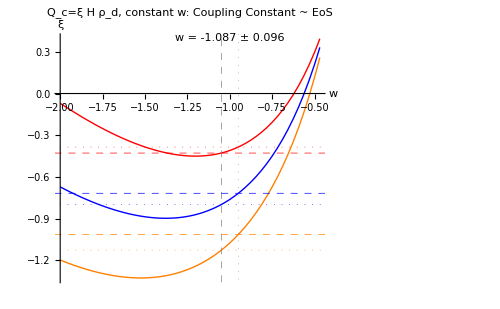

```mathematica
pltξvwExam1I2CC
```

Or we can use some fitting results from WMAP etc. Take the example of w=-1.087±0.096.

```mathematica
tabξvwExamI2CC
```

Q_c=ξ H ρ_d,Constant w. (Data used:Data From, 2) |  |  | 
w | Center | Lower | Upper
-1.183 | -0.864289 | -1.22984 | -0.449552
-1.087 | -0.820486 | -1.15946 | -0.437339
-0.991 | -0.753634 | -1.06346 | -0.405262

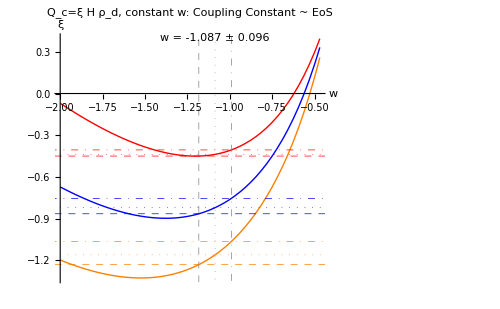

```mathematica
pltξvwExamI2CC
```

Now we assume we do not have the observed Ωm0 data, how do this Ωm0 change the result. In other words, if the observed Ωm0 data float around some value, then how is the fitting result? We also consider the curvature.

```mathematica
pltξvΩm0I2CCManSum
```

If Ωm0 varies 0.05 percent from 0.274,

```mathematica
tabξI2CCSum
```

For Ωm0∈0.274 (1±0.05) Table of ξ for different Ωm0~Transition combination |  |  | 
Ωm0Transition | 0.426 | 0.376 | 0.508
0.2603 | -0.832284 | -1.07758 | -0.53584
0.274 | -0.760999 | -1.00068 | -0.471298
0.2877 | -0.688664 | -0.922602 | -0.40585

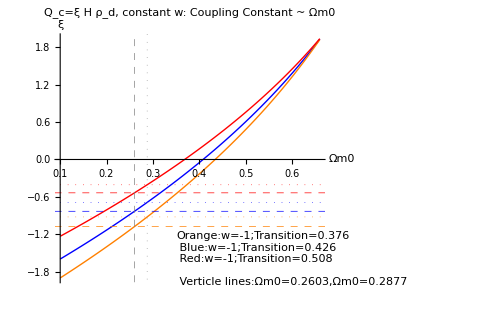

```mathematica
pltξvΩm0I2CCSum
```

In addition, we can also find out the effects of Curvature, EoS. Assuming we have a constrain of Transition redshift (0.376,0.508) with a center at 0.426.

```mathematica
fitξ2I2CCManSum
```

### References

#### Data From

CPL data

Combining SN1a, BAO 3, WMAP5, H(z)   (From arXiv:0909.0596)

Ωm0=0.269_-0.008^(+0.017), w0=-0.97_-0.07^(+0.12), w1=0.03_-0.75^(+0.26).

LCDM

From WMAP: Ωm0=0.265
arXiv:astro-ph/0611572, Riess et al     : 
arXiv:1205.4688 : Ωm0=0.247 (+0.013, -0.013)  and Transition 0.426 (+0.082, -0.050)

Equation of state

From arXiv:1202.0545v1
w = -1.087±0.096.